## Taking a picture

This is just taking a picture using your webcam

```mathematica
Button["Take photo",
image=CurrentImage[];
]
Dynamic@image
```

Take photo

## Machine Learning basics

```mathematica
Column[1+RandomReal[{-.25,.25}]->"one"&/@Range[10]]
```

1.22335→one
0.913005→one
1.06788→one
1.13075→one
1.12283→one
0.840181→one
0.943618→one
1.16638→one
0.866447→one
1.18285→one

```mathematica
Column[2+RandomReal[{-.25,.25}]->"two"&/@Range[10]]
```

2.23207→two
1.93791→two
1.96324→two
2.16793→two
2.23238→two
1.95846→two
1.90627→two
2.07984→two
1.92846→two
1.82744→two

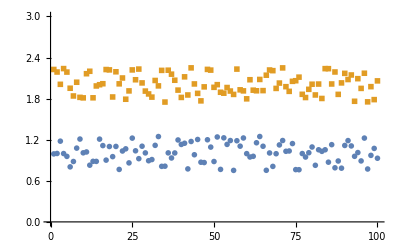

```mathematica
realData1=1+RandomReal[{-.25,.25}]->"one"&/@Range[100];
realData2=2+RandomReal[{-.25,.25}]->"two"&/@Range[100];
values1=Keys[Association@@realData1];
values2=Keys[Association@@realData2];
ListPlot[{values1,values2},PlotRange->{0,3},PlotMarkers->{Automatic,Small}]
```

```mathematica
data=Flatten@Join@{realData1,realData2};
thinkingMachine=Classify@data
```

ClassifierFunction[…]

```mathematica
thinkingMachine@1.1
```

one

```mathematica
thinkingMachine@0.8
```

one

```mathematica
thinkingMachine@1.89
```

two

```mathematica
testData=RandomReal[{0,3},1000];
```

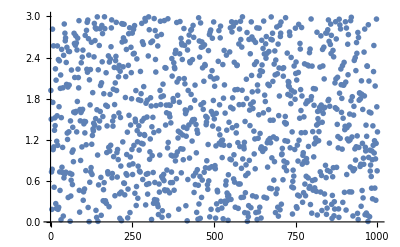

```mathematica
ListPlot[testData,PlotRange->{0,3},PlotMarkers->{Automatic,Small}]
```

```mathematica
understanding=Map[{#,thinkingMachine@#}&,testData];
Column@understanding[[1;;10]]
```

{1.91978,two}
{1.49902,one}
{0.729802,one}
{0.182533,one}
{0.768567,one}
{2.81443,two}
{1.74523,two}
{1.05537,one}
{2.5706,two}
{1.09541,one}

```mathematica
ones=First/@Cases[understanding,{_,"one"}];
twos=First/@Cases[understanding,{_,"two"}];
```

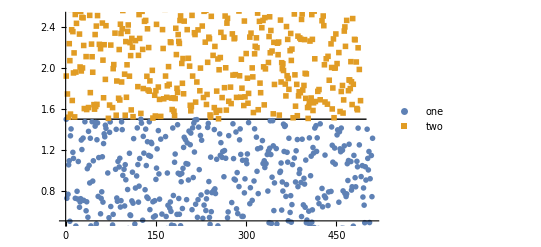

```mathematica
ListPlot[{Legended[ones,"one"],Legended[twos,"two"]},PlotRange->{.5,2.5},Epilog->Line[{{0,1.5},{500,1.5}}],PlotMarkers->{Automatic,Small}]
```

## Let’s teach the computer to see something!

```mathematica
object1={};
Button["Add photo of object1",
AppendTo[object1,CurrentImage[]]
]
Dynamic@Length@object1
```

Add photo of object1

```mathematica
object2={};
Button["Add photo of object2",
AppendTo[object2,CurrentImage[]]
]
Dynamic@Length@object2
```

Add photo of object2

```mathematica
ImageCollage@object1[[1;;4]]
```

-Graphics-

```mathematica
ImageCollage@object2[[1;;4]]
```

-Graphics-

```mathematica
Button["Teach Computer",
message="thinking...";
ts1=#->"object1"&/@object1;
ts2=#->"object2"&/@object2;
discern=Classify[Flatten@Join@{ts1,ts2}];
message="Eureka! I think I understand";,
Method->"Queued"
]
Dynamic@message
```

Teach Computer

```mathematica
Button["Test Computer",
testImage=CurrentImage[];
conclusion=discern@testImage;
]
Dynamic@testImage
Dynamic@conclusion
```

Test Computer

## How smart is Mathematica?

```mathematica
DynamicModule[
{image,item,pts},
Column[{
Button["Identify Image",
image=CurrentImage[];
item=ImageIdentify@image;
(*pts=HighlightImage[image,ImageKeypoints@image]*);,
Method->"Queued"
],
Dynamic@image,
Dynamic@item(*,
Dynamic@pts*)
}]
]
```

## Using indico

```mathematica
Get["https://raw.githubusercontent.com/IndicoDataSolutions/indicoio-mathematica/master/indico.wl"];
apiKey="fdd0144bfe641673064a6a20d59a35a4";
```

```mathematica
indico[][[1;;8]]
```

{Sentiment,SentimentHQ,Language,Political,TextTags,Keywords,NamedEntities,TwitterEngagement}

```mathematica
DynamicModule[
{api,text,result},
Column[{
PopupMenu[Dynamic@api,indico[][[1;;8]]],
InputField[Dynamic@text,String],
Button["Run API",
result=indico[api,text,"Probabilities","TopN"->5];,
Method->"Queued"
],
Dynamic@Column@Normal@result
}]
]
```